```mathematica
diceOutcome[n_]:=1/6^n CoefficientList[((1-x^6)/(1-x)x)^n,x][[n+1;;]]
barColor=RGBColor[0.529,0.808,0.922];
```

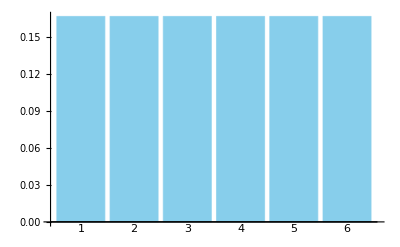

```mathematica
p1=With[{n=1},BarChart[diceOutcome[n],ChartLabels->Range[n,6n],LabelStyle->Directive[Black,Bold,12],ChartStyle->barColor,TicksStyle->Directive[Black,Bold, 12]]]
Export["D:\\website\\CLT_plots\\dice1.png",p1,ImageResolution->100];
```

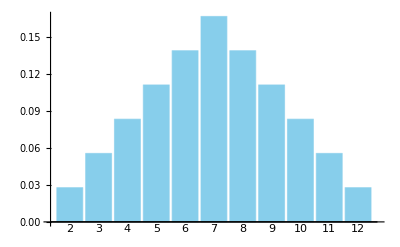

```mathematica
p2=With[{n=2},BarChart[diceOutcome[n],ChartLabels->Range[n,6n],LabelStyle->Directive[Black,Bold,12],ChartStyle->barColor,TicksStyle->Directive[Black,Bold, 12]]]
Export["D:\\website\\CLT_plots\\dice2.png",p2,ImageResolution->100];
```

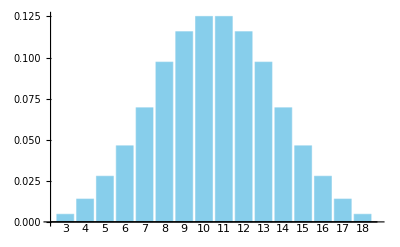

```mathematica
p3=With[{n=3},BarChart[diceOutcome[n],ChartLabels->Range[n,6n],LabelStyle->Directive[Black,Bold,12],ChartStyle->barColor,TicksStyle->Directive[Black,Bold, 12]]]
Export["D:\\website\\CLT_plots\\dice3.png",p3,ImageResolution->100];
```

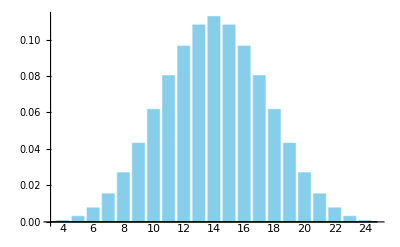

```mathematica
p4=With[{n=4},BarChart[diceOutcome[n],ChartLabels->Table[If[EvenQ@i,i,""],{i,n,6n}],LabelStyle->Directive[Black,Bold,12],ChartStyle->barColor,TicksStyle->Directive[Black,Bold, 12]]]
Export["D:\\website\\CLT_plots\\dice4.png",p4,ImageResolution->100];
```

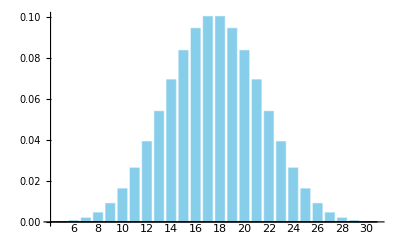

```mathematica
p5=With[{n=5},BarChart[diceOutcome[n],ChartLabels->Table[If[EvenQ@i,i,""],{i,n,6n}],LabelStyle->Directive[Black,Bold,12],ChartStyle->barColor,TicksStyle->Directive[Black,Bold, 12]]]
Export["D:\\website\\CLT_plots\\dice5.png",p5,ImageResolution->100];
```

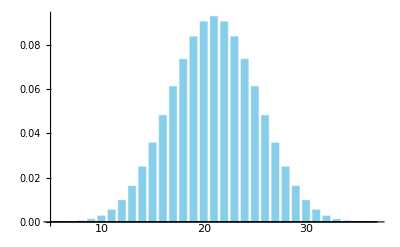

```mathematica
p6=With[{n=6},BarChart[diceOutcome[n],ChartLabels->Table[If[Mod[i,10]==0,i,""],{i,n,6n}],LabelStyle->Directive[Black,Bold,12],ChartStyle->barColor,TicksStyle->Directive[Black,Bold, 12]]]
Export["D:\\website\\CLT_plots\\dice6.png",p6,ImageResolution->100];
```

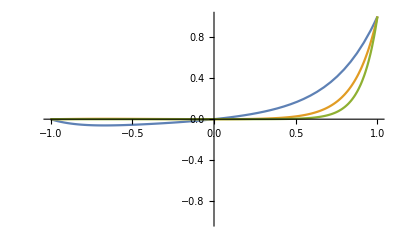

```mathematica
Plot[{1/6 x(1-x^6)/(1-x),1/6^2(x(1-x^6)/(1-x))^2,1/6^3(x(1-x^6)/(1-x))^3},{x,-1,1},PlotRange->{-1,1}]
```

```mathematica
SeriesCoefficient[((1-x^6)/(1-x))^n,{x,0,k}]
```

Piecewise[{{DifferenceRoot[Function[{y,n},{(n-5 n) y[n]+(1+n-4 n) y[1+n]+(2+n-3 n) y[2+n]+(3+n-2 n) y[3+n]+(4+n-n) y[4+n]+(5+n) y[5+n]==0,y[0]==1,y[1]==n,y[2]==1/2 n (1+n),y[3]==1/6 n (2+3 n+n^2),y[4]==1/24 n (6+11 n+6 n^2+n^3)}]][k], k≥0}, {0, True}}]

```mathematica
D[1/(1-x),{x,3}]
```

6/(1-x)^4

```mathematica
With[{n=5},D[1/((n-1)!)x^(n-1),{x,n-1}]]
With[{n=5},D[1/((n-1)!)x^n,{x,n-1}]]
With[{n=5},D[1/((n-1)!)x^(n+1),{x,n-1}]]
With[{n=5},D[1/((n-1)!)x^(n+2),{x,n-1}]]
With[{n=5},D[1/((n-1)!)x^(n+3),{x,n-1}]]
With[{n=5},D[1/((n-1)!)x^(n+4),{x,n-1}]]
```

1

5 x

15 x^2

35 x^3

70 x^4

126 x^5

```mathematica
D[x^n((1-x^6)/(1-x))^n,x]//Simplify
```

n x^(-1+n) (1+x+x^2+x^3+x^4+x^5)^(-1+n) (1+2 x+3 x^2+4 x^3+5 x^4+6 x^5)

```mathematica
1/6^n n x^(-1+n) (1+x+x^2+x^3+x^4+x^5)^(-1+n) (1+2 x+3 x^2+4 x^3+5 x^4+6 x^5)/.x->1
```

(7 n)/2

```mathematica
D[x D[x^n((1-x^d)/(1-x))^n,x],x]//Simplify
```

(n x^(-1+n) ((-1+x^d)/(-1+x))^n (x-d^2 x^d+2 (-1+d^2) x^(1+d)-d^2 x^(2+d)+x^(1+2 d)+n (1-(1+d) x^d+d x^(1+d))^2))/((-1+x)^2 (-1+x^d)^2)

```mathematica
Limit[(n x^(-1+n) ((-1+x^d)/(-1+x))^n (x-d^2 x^d+2 (-1+d^2) x^(1+d)-d^2 x^(2+d)+x^(1+2 d)+n (1-(1+d) x^d+d x^(1+d))^2))/((-1+x)^2 (-1+x^d)^2),x->1]
```

1/12 d^n (1+d) n (-1+d+3 n+3 d n)

```mathematica
1/d^n 1/12 d^n (1+d) n (-1+d+3 n+3 d n)-((d+1)/2 n)^2//Simplify
```

1/12 (-1+d^2) n

```mathematica
1/12 (-1+d^2) n
```

7/12 n (-21 n+6^n (5+21 n))

```mathematica
Series[(2+2 d^2+5 n-5 d^2 n)/(40 n-40 d^2 n),{n,Infinity,8}]//Simplify
Series[(-16 (1+d^2+d^4)+42 (-1+d^4) n-35 (-1+d^2)^2 n^2)/(1680 (-1+d^2)^2 n^2),{n,Infinity,8}]//Simplify
```

1/8+(1+d^2)/((20-20 d^2) n)+O[1/n]^9

-1/48+(1+d^2)/(40 (-1+d^2) n)-(1+d^2+d^4)/(105 (-1+d^2)^2 n^2)+O[1/n]^9

```mathematica
Series[1/6^n E^(I n t)((1-E^(6I t))/(1-E^(I t)))^n,{t,0,2}]
With[{μ=(d+1)/2 n,σ=√((d^2-1)/12 n)},Series[Exp[-I μ t/σ]/d^n E^(I n t/σ)((1-E^(d I t/σ))/(1-E^(I t/σ)))^n,{t,0,8}]]//FullSimplify
```

1+(7 ⅈ n t)/2-7/24 (5 n+21 n^2) t^2+O[t]^3

1-t^2/2+((2+2 d^2+5 n-5 d^2 n) t^4)/(40 n-40 d^2 n)+((-16 (1+d^2+d^4)+42 (-1+d^4) n-35 (-1+d^2)^2 n^2) t^6)/(1680 (-1+d^2)^2 n^2)+((-144 (1+d^2) (1+d^4)+4 (-101-21 d^2+21 d^4+101 d^6) n-420 (-1+d^2)^2 (1+d^2) n^2+175 (-1+d^2)^3 n^3) t^8)/(67200 (-1+d^2)^3 n^3)+O[t]^9

```mathematica
With[{μ=(d+1)/2 n,σ=√((d^2-1)/12 n)},Integrate[Exp[-I μ t/σ] E^(I n t/σ)/d^n((1-E^(dI t/σ))/(1-E^(I t/σ)))^n E^(-I t y),{t,-Infinity,Infinity},Assumptions->{n>1,Element[y,Reals]}]]
```

Integrate[6^-n ⅇ^(2 ⅈ √(3/35) √n t-ⅈ √(21/5) √n t-ⅈ t y) ((1-ⅇ^((12 ⅈ √(3/35) t)/(√n)))/(1-ⅇ^((2 ⅈ √(3/35) t)/(√n))))^n,{t,-∞,∞},Assumptions→{n>1,y∈ℝ}]

```mathematica
With[{μ=7/2 n,σ=√(35/12 n)},Simplify[Exp[-I μ t/σ] E^(I n t/σ)/6^n((1-E^(6I t/σ))/(1-E^(I t/σ)))^n]]
```

6^-n ⅇ^(-ⅈ √(15/7) √n t) (-(-1+ⅇ^((12 ⅈ √(3/35) t)/(√n)))/(1-ⅇ^((2 ⅈ √(3/35) t)/(√n))))^n

```mathematica
FullSimplify[Log[E^(I n t/σ)/6^n((1-E^(6I t/σ))/(1-E^(I t/σ)))^n],Assumptions->{n>1,Element[t,Reals]}]
```

Log[6^-n ⅇ^((ⅈ n t)/σ) (-(-1+ⅇ^((6 ⅈ t)/σ))/(1-ⅇ^((ⅈ t)/σ)))^n]

Table::iterb: Iterator {i,n,6 n} does not have appropriate bounds.

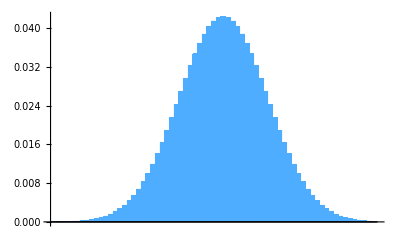

```mathematica
BarChart[data,ChartLabels->Table[If[Mod[i,15]==0,i,""],{i,n,6n}],LabelStyle->Directive[Black,Bold,12],ChartStyle->RGBColor[0.31,0.68,1.],TicksStyle->Directive[Black,Bold, 12]]
```

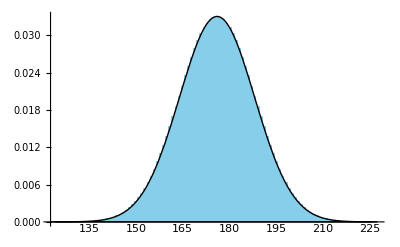

```mathematica
p=With[{n=50},
imin=Max[1,Floor[-n+7n/2-7 √n]];
imax=Min[Ceiling[-n+7n/2+7 √n],5n];
data=diceOutcome[n][[imin;;imax]];
Show[BarChart[data,ChartLabels->Table[If[Mod[imin+i,15]==0,imin+i,""],{i,n,6n}],LabelStyle->Directive[Black,Bold,12],ChartStyle->barColor,TicksStyle->Directive[Black,Bold, 12]],Plot[1/(√(2π 35n/12))Exp[-(-2+n+imin+x-7n/2)^2/(2 35n/12)],{x,0,7n/2+7 √n-imin-n+2},PlotStyle->{Black,Thick}]]]
Export["D:\\website\\CLT_plots\\dice50.png",p,ImageResolution->100];
```